# Introduction to Mathematical Epidemiology

Notes to accompany course material for PH252B

## Ch 2: Introduction to Epidemic Modeling

### 2.1 Kermack-McKendrick SIR Epidemic Model

```mathematica
SIRclosed={
S'[t]==-β i[t] S[t],
i'[t]==β i[t] S[t]-α i[t],
R'[t]==α i[t],
S[0]==100-1,i[0]==1,R[0]==0
};
{β,α,tmax}={.01,1/2,100};
SIRcloseSoln=NDSolve[SIRclosed,{S,i,R},{t,0,tmax}];
```

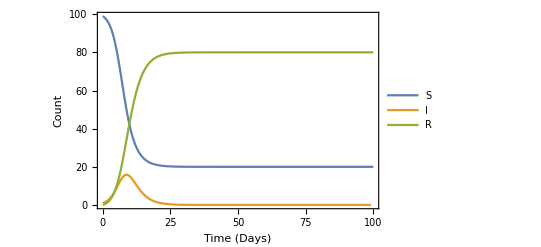

```mathematica
Plot[
{
S[t]/.SIRcloseSoln,
i[t]/.SIRcloseSoln,
R[t]/.SIRcloseSoln
},
{t,0,tmax},Frame->True,PlotLegends->Flatten[{"S","I","R"}],FrameLabel->{"Time (Days)","Count"},PlotRange->{0,All}
]
```

One can also calculate the final size of the epidemic

```mathematica
99*ⅇ^(-β/α 100)
```

13.3982

As well as maximum severity of epidemic

```mathematica
-α/β+α/β Log[α/β]+99+1-α/β Log[99]
```

15.8452

### 2.2 Estimating Parameters from Data

We note that the number of individuals in the I class at any time t is given by an exponential function; thus for a given cohort of infecteds, the fraction of individuals who have left the infected compartment is given by the exponential distribution parameterized by alpha; mean time spent in the infectious class is the inverse of alpha.

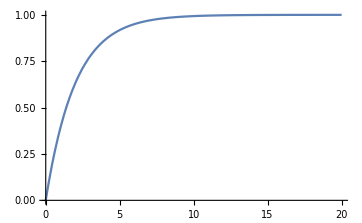

```mathematica
Plot[1-ⅇ^(-α x),{x,0,20},PlotRange->All]
```

### 2.3 A Simple SIS Epidemic Model